# Introduction To Mathematica

## Part1

Notes from the Mathematica intro screencast www.wolfram.com/broadcast/screencasts/handsonstart Futher Mathematica information is available from the build in help system (including editable example code) found under Help -> Documentation Center

## Some Calculations

Mathematica calculatex exactly unless told otherwhise

```mathematica
224 / 24248
```

4/433

```mathematica
224.0/24248
```

0.00923788

```mathematica
N[224/24248]
```

0.00923788

we can also refer to the last result

```mathematica
224/24248
```

4/433

```mathematica
N[%]
```

0.00923788

and we can save a result in a variable and scale the approximation

```mathematica
divprob = 224/24248
```

4/433

```mathematica
N[divprob, 3]
```

0.00924

## Basic Math

Mathematica follows three simple rules

1. Captial letters - function names (names spelled correctly are in black otherwise dark blue)
2. [] - anything we want to calculate
3. {} - lists or range

We can factor polynomials

```mathematica
Factor[a^2 + 2a+1]
```

(a+1)^2

and we can integrate with respect to variable a

```mathematica
Integrate[a^2 + 2a + 1,a]
```

a^3/3+a^2+a

and we can generate function date by specifying input range

```mathematica
Table[a^2 + 1, {a, 1, 10}]
```

{2,5,10,17,26,37,50,65,82,101}

We can also input math graphically by going to Palettes -> Classroom Assistant (also set TraditionalForm under Preferences -> Evaluation -> Output Form). Fonts can be controled by opening Format -> Show Fints (Shortcut: Command - T)

```mathematica
∫1/(1-x^3)ⅆx
```

1/6 log(x^2+x+1)-1/3 log(x-1)+(tan^-1((2 x+1)/(√3)))/(√3)

## Basic Plotting

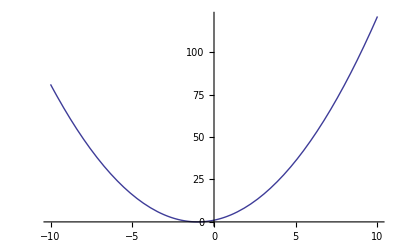

```mathematica
Plot[a^2 + 2a + 1, {a, -10, 10}]
```

use the Ctrl / key combination to create a fraction

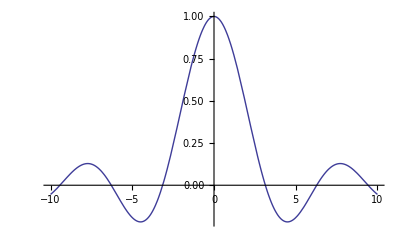

```mathematica
Plot[Sin[x]/x,{x, -10, 10}]
```

You can fine tune your graphics via the Graphics menu (Drawing Tools and Graphics Inspector).

```mathematica
Plot[Sin[x]/x,{x, -10, 10}]
```

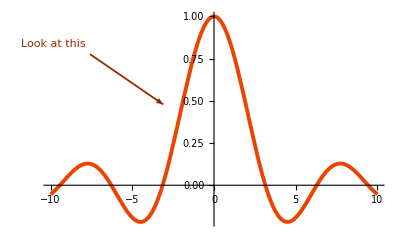

We can also build models (π is created by hitting Escape-pi-Escape)

```mathematica
Manipulate[Plot[Sin[freq x], {x, -2π,2π}],{freq, 1, 5}]
```

3 D plotting is easy as well ( Click the graphic to rotate it, Click-while-pressing-Command to zoom it)

```mathematica
Plot3D[Sin[x*y]/x,{x, -3, 3},{y,-3, 3}]
```

-Graphics3D-

Countur plots are possible as well

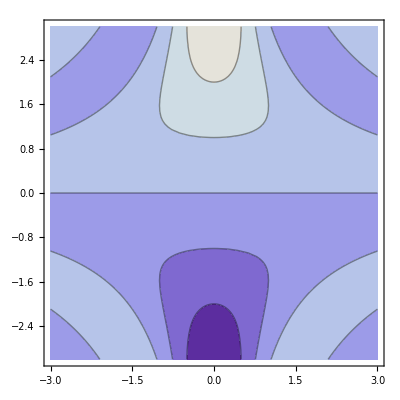

```mathematica
ContourPlot[Sin[x*y]/x,{x, -3, 3},{y,-3, 3}]
```